# Ramsey Numbers

Ramsey’s Theorem states that, for a sufficiently large complete graph, any coloring of the edges yields a monochromatic clique. Ramsey Numbers, written R(r,s), give the minimum number of vertices that a complete graph must contain such that the graph contains either an r-clique of one color or an s-clique of the other color.

## Complete Graphs

A complete graph K_n is a set of n vertices and (n(n-1))/2 edges such that each pair of distinct vertices is joined by an edge.

Draw a set of complete graphs on 3, 4, 5 and 6 vertices.


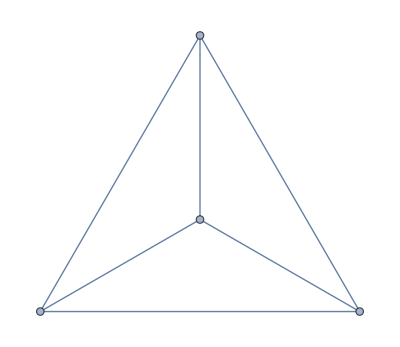

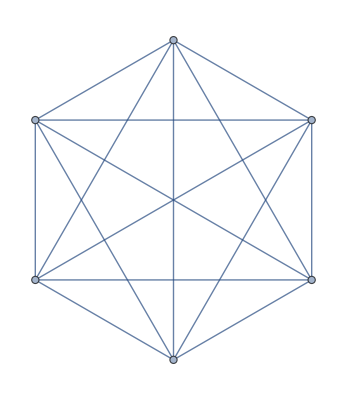

```mathematica
Table[ CompleteGraph[ n ], {n, 3, 6} ]
```

Notice that in general, the complete graph on n vertices requires exactly (n(n-1))/2 edges in order to connect each distinct pair of vertices by a unique edge.

## Graph Edge Coloring

We can divide the set E of edges of a graph G into disjoint subsets of edges by using colors; each subset is then composed of edges of a particular color. 

For example, we can use 2 colors, red and blue, to color the edges of K_6, the complete graph on 6 vertices. The vertices are labeled 1 through 6, and an edge joining vertices i and j is denoted by i <-> j.

Randomly choose a (nonempty) subset of edges to color red.

```mathematica
redEdges = RandomChoice[ EdgeList[ CompleteGraph[6] ], RandomInteger[ {1, 15} ] ]
```

{2<->4,4<->5,2<->6,2<->4,1<->4,1<->3,1<->5}

The set of blue edges is the complement of the set of red edges.

```mathematica
blueEdges = Complement[ EdgeList[ CompleteGraph[6] ], redEdges ]
```

{1<->2,1<->6,2<->3,2<->5,3<->4,3<->5,3<->6,4<->6,5<->6}

Finally, draw the complete graph with the appropriately colored edges.

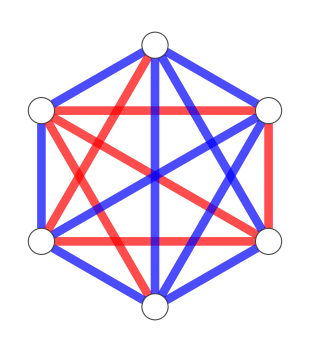

```mathematica
coloredK6 = CompleteGraph[6,
				BaseStyle -> Directive[ Blue, Thickness -> 0.02 ], 
				EdgeStyle -> Table[ edge -> Red, { edge, redEdges } ],
				VertexLabels -> Placed[ Automatic, Center ],
				VertexSize -> Medium, 
				VertexStyle -> White,
				VertexLabelStyle -> Directive[ Bold, 14 ]
				]
```

## Monochromatic Cliques

A monochromatic clique is a subgraph H of some graph G that is itself a complete graph, and in which all edges are the same color. That is, it is a graph on a subset of the vertices of H such that every distinct pair of vertices is connected by an edge, and the entire graph contains only one color.

Examples of monochromatic cliques in the graph above.

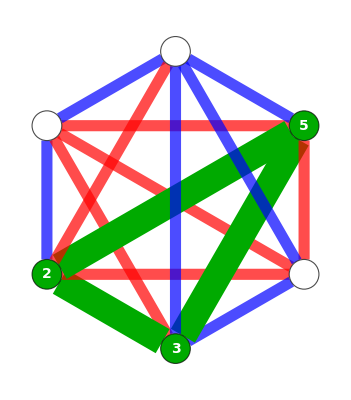
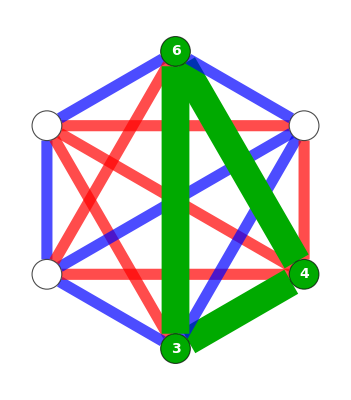
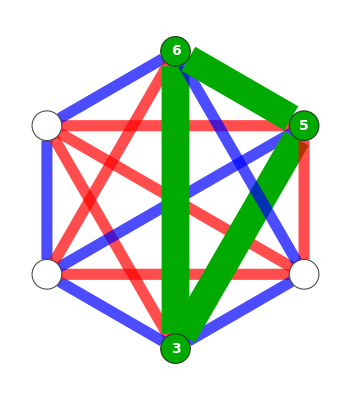
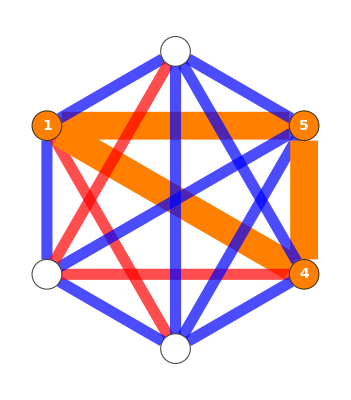

```mathematica
MapThread[
    Table[ 
        HighlightGraph[
            coloredK6,
            Style[ 
                Subgraph[#1, clique],
                Directive[#2, "Thickness" -> .05, Opacity[1] ]
            ]
        ],
        {clique, FindClique[#1, { 3, Infinity }, All ]}
    ]&,
    {{blueEdges, redEdges}, {Darker[Green], Orange}}
]
```

In the above image, monochromatic cliques are highlighted. Green-highlighted edges correspond to blue monochromatic cliques, and orange-highlighted edges correspond to red monochromatic cliques. Note that if a monochromatic clique contains 3 or more vertices, then it also contains as subgraphs all monochromatic cliques of fewer vertices. 

If there are no cliques shown of either green or orange, then the graph contains no monochromatic cliques corresponding color.

## Ramsey’s Theorem and Ramsey Numbers

The main statement Ramsey’s theorem makes is that, if a complete graph is large enough, then no matter how the edges are colored, we will always be able to find a monochromatic clique contained in the graph. 

The Ramsey Numbers R( r, s ) give the smallest number of vertices that must be contained in a graph so that the graph contains a clique on r vertices of one color (say, red), or a clique on s vertices of the other color (blue).

## R( 3 , 3 ) = 6

For example, the Ramsey Number R( 3, 3 ) = 6. That is, the smallest complete 2-colored graph that is guaranteed to contain a monochromatic clique of 3 vertices, no matter how the graph is colored, has 6 vertices.

To see this firsthand, we can try to 2-color K_6 in any way. Notice that every coloring will always yield at least one clique of at least 3 vertices.

Find the full edge set of K_6.

```mathematica
allEdges6 = EdgeList[ CompleteGraph[6] ]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6}

Use the toggle bar to turn particular edges red. The toggle button labels “ i <-> j ” correspond to the edge between the vertices labeled with numbers i and j.

Draw a dynamic, 2-colorable K_6.

```mathematica
edgeStrings = Flatten[ Table[ ToString[ j <-> i ], {i, 1, 6}, {j, 1, i - 1} ] ];

DynamicModule[{ r = {} },
	Row[{
		CheckboxBar[ 
			Dynamic[r], 
			Table[i -> edgeStrings[[i]], {i, Range[15]}],
			Appearance -> "Vertical" -> {Automatic, Automatic}
		],
		Dynamic[ 
			CompleteGraph[ 6,
				BaseStyle -> Directive[ Blue, Thickness -> 0.03, Opacity[1] ], 
				EdgeStyle -> Table[ edge -> Red, {edge, Part[ allEdges6, r ]}],
				VertexSize -> Medium,
				VertexStyle -> White,
				VertexLabels -> Placed[ Automatic, Center ],
				VertexLabelStyle -> Directive[ Bold, 20 ],
				ImageSize -> Medium
			]
		]
	}]
]
```

This shows that R( 3, 3 )≤ 6, since the minimum size of a complete graph with a guaranteed 3-clique is no larger than 6. 

Moreover, if we consider the following graph, we can see that R( 3, 3 ) > 5, since there exists a way to color K_5, the complete graph on 5 vertices, so that there are no cliques of at least 3 vertices.

Draw a coloring of K_5 with no 3-cliques.

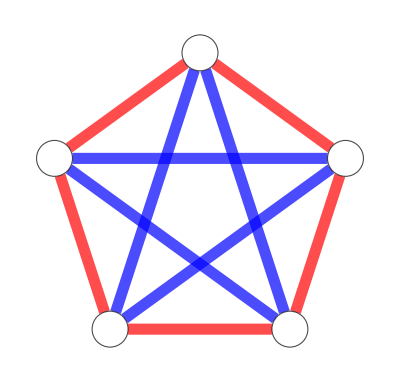

```mathematica
CompleteGraph[5,
				BaseStyle -> Directive[ Blue, Thickness -> 0.02 ], 
				EdgeStyle -> Table[ edge -> Red, { edge, { 1<->2, 2<->3, 3<->4, 4<->5, 5<->1 } } ],
				VertexLabels -> Placed[ Automatic, Center ],
				VertexSize -> Medium, 
				VertexStyle -> White,
				VertexLabelStyle -> Directive[ Bold, 14 ]
				]
```

Thus, we conclude that since 5 < R( 3, 3) ≤ 6, we must have that R( 3, 3) = 6.

## Ramsey Numbers Are Hard to Find!

Although Ramsey Theory -- the branch of mathematics that studies Ramsey’s Theorem and related problems -- is relatively little-known, after a little thinking and visualization, the fundamental idea seems pretty straightforward. 

However, it turns out that for all its intuitive graphical representation, finding Ramsey Numbers, even for small r and s, is extremely difficult. In fact, R(4, 5) = 25 was only discovered in 1995, and we still don’t know the exact value of R(5, 5) - though we know it’s between 43 and 48. As for R(6, 6), here’s what the great mathematician Paul Erdős famously had to say about it:

	“Suppose aliens invade the earth and threaten to obliterate it in a year’s time unless human beings can find the Ramsey number for red five and blue five. We could marshal the world’s best minds and fastest computers, and within a year we could probably calculate the value. If the aliens demanded the Ramsey number for red six and blue six, however, we would have no choice but to launch a preemptive attack.”
	
	- Paul Erdős, as quoted in “Ramsey Theory” by Ronald L. Graham and Joel H. Spencer, in Scientific American (July 1990), p. 112-117

Authorship information

Hikari Sorensen

2017/06/22

laurensorensen@college.harvard.edu